# Schwinger Effect in de Sitter Space - Conformal Time Coordinates

## Lagrangian:

For a free particle in de Sitter space, the Lagrangian (in conformal time coordinates) is:

```mathematica
η'[T]D[-1/(λ^2 η[T]),T] (*Product of first terms of each vector*)
```

η'[T]^2/(λ^2 η[T]^2)

```mathematica
x'[T] D[x[T]/(λ η[T])^2,T](*Product of second terms of each vector*)
```

x'[T] (x'[T]/(λ^2 η[T]^2)-(2 x[T] η'[T])/(λ^2 η[T]^3))

```mathematica
FullSimplify[η'[T]D[-1/(λ^2 η[T]),T]+x'[T] D[x[T]/(λ η[T])^2,T]] (* Product of both vectors *)
```

(-2 x[T] x'[T] η'[T]+η[T] (x'[T]^2+η'[T]^2))/(λ^2 η[T]^3)

```mathematica
LC=FullSimplify[m/(2n)((-η'[T]^2)/(λ η[T])^2+x'[T]^2/(λ η[T])^2)-(m n)/2] (* The Lagrangian *)
```

-(m (n^2 λ^2 η[T]^2-x'[T]^2+η'[T]^2))/(2 n λ^2 η[T]^2)

## Let’s test all the derivatives and see if we get the right results:

## Partials wrt x

```mathematica
D[LC,x[T]]
D[LC,x'[T]]
```

0

(m x'[T])/(n λ^2 η[T]^2)

```mathematica
D[D[LC,x'[T]],T]
```

-(2 m x'[T] η'[T])/(n λ^2 η[T]^3)+(m x''[T])/(n λ^2 η[T]^2)

## Partials wrt η

```mathematica
D[LC,η[T]]
D[LC,η'[T]]
```

-(m n)/η[T]+(m (n^2 λ^2 η[T]^2-x'[T]^2+η'[T]^2))/(n λ^2 η[T]^3)

-(m η'[T])/(n λ^2 η[T]^2)

```mathematica
D[D[LC,η'[T]],T]
```

(2 m η'[T]^2)/(n λ^2 η[T]^3)-(m η''[T])/(n λ^2 η[T]^2)

Yes we do!

## Find the equations of motion:

```mathematica
xeqc =FullSimplify[D[D[LC,x'[T]],T]-D[LC,x[T]]==0, Assumptions->{m>0,n>0,λ>0}]
```

x''[T]==(2 x'[T] η'[T])/η[T]

```mathematica
teqc=FullSimplify[D[D[LC,η'[T]],T]-D[LC,η[T]]==0, Assumptions->{m>0,n>0,λ>0}]
```

η''[T]==(x'[T]^2+η'[T]^2)/η[T]

### Reparametrized equations:

```mathematica
teqr=FullSimplify[η''[T]==(2 η'[T]^2-(λ n η[T])^2)/η[T]](* Simplifying reparametrization *)
```

n^2 λ^2 η[T]+η''[T]==(2 η'[T]^2)/η[T]

```mathematica
η[T]->FullSimplify[((Exp[λ*T]*EB*(Exp[2*λ]-1)*EA)/(EA*Exp[2*λ*T]*Exp[λ]-EA*Exp[λ]-EB*Exp[2*λ*T]+EB*Exp[2*λ])) ](* Solution of teqr *)
```

η[T]→(EA EB Sinh[λ])/(EA Sinh[T λ]+EB Sinh[λ-T λ])

```mathematica
η'[T]->D[ (η[T]/.η[T]->(ⅇ^(T λ) (-1+ⅇ^(2 λ)) EA EB)/(-ⅇ^λ EA+ⅇ^(λ+2 T λ) EA+ⅇ^(2 λ) EB-ⅇ^(2 T λ) EB)),T] (* Because Mathematica is being dumb *)
```

η'[T]→(ⅇ^(T λ) (-1+ⅇ^(2 λ)) EA EB λ)/(-ⅇ^λ EA+ⅇ^(λ+2 T λ) EA+ⅇ^(2 λ) EB-ⅇ^(2 T λ) EB)-(ⅇ^(T λ) (-1+ⅇ^(2 λ)) EA EB (2 ⅇ^(λ+2 T λ) EA λ-2 ⅇ^(2 T λ) EB λ))/((-ⅇ^λ EA+ⅇ^(λ+2 T λ) EA+ⅇ^(2 λ) EB-ⅇ^(2 T λ) EB)^2)

```mathematica
x''[T]==FullSimplify[(2 x'[T]*D[ (η[T]/.η[T]->(ⅇ^(T λ) (-1+ⅇ^(2 λ)) EA EB)/(-ⅇ^λ EA+ⅇ^(λ+2 T λ) EA+ⅇ^(2 λ) EB-ⅇ^(2 T λ) EB)),T])/η[T]//.η[T]->(ⅇ^(T λ) (-1+ⅇ^(2 λ)) EA EB)/(-ⅇ^λ EA+ⅇ^(λ+2 T λ) EA+ⅇ^(2 λ) EB-ⅇ^(2 T λ) EB)] (* Substituting η(T) into xeqc *)
```

x''[T]==(2 λ (-EA Cosh[T λ]+EB Cosh[λ-T λ]) x'[T])/(EA Sinh[T λ]+EB Sinh[λ-T λ])

## Solve the equation of motion to get x(T) and η(T):

### Attempt at reparametrizatized solutions:

```mathematica
Clear[solxr,soltr]
```

```mathematica
solxr[T_]:=FullSimplify[(-EA*EB*Exp[2*λ*(T+1)]*XB-EB^2*Exp[3*λ]*XA+EA*EB*Exp[2*λ]*XA+EA*EB*Exp[2*λ]*XB+EB^2*Exp[λ*(2*T+1)]*XA+EA^2*Exp[λ*(2*T+1)]*XB-EA^2*Exp[λ]*XB-EA*EB*Exp[2*λ*T]*XA)/((-EB*Exp[λ]+EA)*(EA*Exp[λ*(2*T+1)]-EA*Exp[λ]-EB*Exp[2*λ*T]+EB*Exp[2*λ]))]
```

```mathematica
soltr[T_]:=FullSimplify[(EA EB Sinh[λ])/(EA Sinh[T λ]+EB Sinh[λ-T λ])]
```

```mathematica
solt=DSolve[{ η''[T]==(2 η'[T]^2-(λ n η[T])^2)/η[T],η[0]==EA,η[1]==EB},η,T,Assumptions->{n>0,λ>0,η[T]≥1}];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
Factor[FullSimplify[η[T]/.solt[[1]],Trig->True]]
```

(EA EB Sech[n T λ-ArcCosh[(EB Sinh[n λ])/(√(-EA^2-EB^2+2 EA EB Cosh[n λ]))]] Sinh[n λ])/(√(-EA^2-EB^2+2 EA EB Cosh[n λ]))

```mathematica
η'[T]->D[ (η[T]/.η[T]->(EA EB Sech[n T λ-ArcCosh[(EB Sinh[n λ])/(√(-EA^2-EB^2+2 EA EB Cosh[n λ]))]] Sinh[n λ])/(√(-EA^2-EB^2+2 EA EB Cosh[n λ]))),T]
```

η'[T]→-(EA EB n λ Sech[n T λ-ArcCosh[(EB Sinh[n λ])/(√(-EA^2-EB^2+2 EA EB Cosh[n λ]))]] Sinh[n λ] Tanh[n T λ-ArcCosh[(EB Sinh[n λ])/(√(-EA^2-EB^2+2 EA EB Cosh[n λ]))]])/(√(-EA^2-EB^2+2 EA EB Cosh[n λ]))

```mathematica
x''[T]==FullSimplify[(2 x'[T]*D[ (η[T]/.η[T]->(EA EB Sech[n T λ-ArcCosh[(EB Sinh[n λ])/(√(-EA^2-EB^2+2 EA EB Cosh[n λ]))]] Sinh[n λ])/(√(-EA^2-EB^2+2 EA EB Cosh[n λ]))),T])/η[T]//.η[T]->(EA EB Sech[n T λ-ArcCosh[(EB Sinh[n λ])/(√(-EA^2-EB^2+2 EA EB Cosh[n λ]))]] Sinh[n λ])/(√(-EA^2-EB^2+2 EA EB Cosh[n λ]))]
```

x''[T]==-2 n λ Tanh[n T λ-ArcCosh[(EB Sinh[n λ])/(√(-EA^2-EB^2+2 EA EB Cosh[n λ]))]] x'[T]

```mathematica
solx=DSolve[{ x''[T]==-2 n λ Tanh[n T λ-ArcCosh[(EB Sinh[n λ])/(√(-EA^2-EB^2+2 EA EB Cosh[n λ]))]] x'[T],x[0]==XA,x[1]==XB},x,T,Assumptions->{n>0,λ>0,EA≥ 1,EB≥ 1}]
```

$Aborted

```mathematica
solxr1[T_]:=
```

```mathematica
soltr1[T_]:=(EA EB Sech[n T λ-ArcCosh[(EB Sinh[n λ])/(√(-EA^2-EB^2+2 EA EB Cosh[n λ]))]] Sinh[n λ])/(√(-EA^2-EB^2+2 EA EB Cosh[n λ]))
```

### Attempt at using general form of solution from Maple: (IGNORE FOR NOW!)

```mathematica
Clear[x,η]
```

```mathematica
x[T_]:=-(2 c2 Sinh[(c3+T)/(2 c1)])/(c1 Cosh[(c3+T)/(2 c1)])+c4
```

```mathematica
repl={x'[T]->D[x[T],T],x''[T]->D[x[T],T,T],x'''[T]->D[x[T],T,T,T],η'[T]->D[η[T],T],η''[T]->D[η[T],T,T],η'''[T]->D[η[T],T,T,T]}
```

{x'[T]→x'[T],x''[T]→x''[T],x^(3)[T]→x^(3)[T],η'[T]→η'[T],η''[T]→η''[T],η^(3)[T]→η^(3)[T]}

```mathematica
η[T]->FullSimplify[-(2 x'[T]^2)/(√(-2 x''[T]^2+2 x'[T] Derivative[3][x][T]))//.x[T]->c4-(2 c2 Tanh[(c3+T)/(2 c1)])/c1//.replacements]
```

η[T]→c1^2 (1+Cosh[(c3+T)/c1]) √(-(c2^2 Sech[(c3+T)/(2 c1)]^6)/c1^6)

```mathematica
η[T_]:=Simplify[-(2 x'[T]^2)/(√(-2 x''[T]^2+2 x'[T] Derivative[3][x][T]))//.x[T]->c4-(2 c2 Tanh[(c3+T)/(2 c1)])/c1//.replacements]
```

```mathematica
Simplify[x[T]]
```

c4-(2 c2 Tanh[(c3+T)/(2 c1)])/c1

```mathematica
Clear[η,x]
```

```mathematica
Assuming[{{c1,c2,c3,c4}∈Reals},Simplify[Solve[x[0]==0 &&x[1]==1 &&η[0]==1 && η[1]==2,{c1,c2,c3,c4} ]]]
```

{}

```mathematica
Solve[x[0]==0 &&x[1]==1 &&η[0]==1 && η[1]==2,{c1,c2,c3,c4} ]
```

$Aborted

## Trajectory plots:

```mathematica
Clear[XA,XB,EA, EB, n(*, m*)];
```

```mathematica
par={XA->1,XB->4,EA-> 1, EB -> 1,λ->-1,n->1(*,m->1*)};
par2={XA->1,XB->4,EA-> 1, EB -> 1,λ->1,n->1(*,m->1,n->1*)};(* Different parameters *)
```

### Simplified expressions for η:

```mathematica
f=soltr1[T]/.par
f2=soltr1[T]/.par2
```

-(Sech[T+ArcCosh[-Sinh[1]/(√(-2+2 Cosh[1]))]] Sinh[1])/(√(-2+2 Cosh[1]))

(Sech[T-ArcCosh[Sinh[1]/(√(-2+2 Cosh[1]))]] Sinh[1])/(√(-2+2 Cosh[1]))

### Simplified expressions for x:

```mathematica
g=solxr1[T]/.par
g2=solxr1[T]/.par2
```

solxr1[T]

solxr1[T]

### Plots of x and t wrt to T :

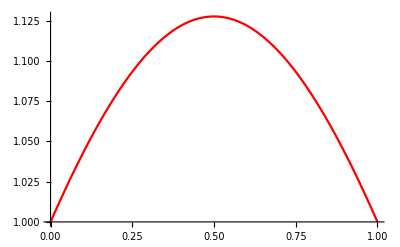

```mathematica
Plot[{f2,g},{T,0,1},PlotStyle->{Red,Green}]
```

#### Trajectory for particle in electric field (t versus x) :

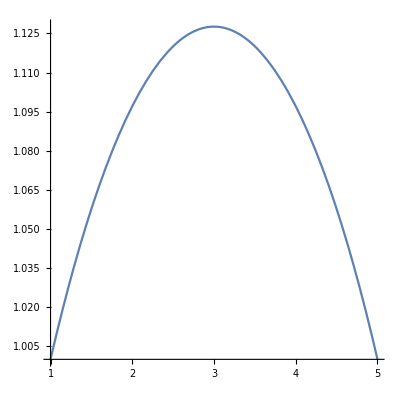

```mathematica
ParametricPlot[{g,f},{T,0,1},AspectRatio->1]
```

### Attempt at Manipulate function:

```mathematica
Clear[xm]
```

```mathematica
(* Variables storing expressions for x and t *)
xm= solxr
```

-1/(2 (-1+ⅇ^((k n)/m)))ⅇ^(-(k n T)/m) (ⅇ^((k n)/m) ta-ⅇ^((k n T)/m) ta+ⅇ^((2 k n T)/m) ta-ⅇ^((k n)/m+(k n T)/m) ta-ⅇ^((k n)/m) tb+ⅇ^((k n T)/m) tb-ⅇ^((2 k n T)/m) tb+ⅇ^((k n)/m+(k n T)/m) tb-ⅇ^((k n)/m) xa+ⅇ^((k n T)/m) xa+ⅇ^((2 k n T)/m) xa-ⅇ^((k n)/m+(k n T)/m) xa+ⅇ^((k n)/m) xb+ⅇ^((k n T)/m) xb-ⅇ^((2 k n T)/m) xb-ⅇ^((k n)/m+(k n T)/m) xb)

```mathematica
(*rep={xa->xaa,xb->xbb,ta->taa,tb->tbb,m->mm,n->nn,k->kk};*)
```

```mathematica
Clear[tm]
```

```mathematica
tm=t[T]/.soltx⟦1⟧
```

-1/(2 (-1+ⅇ^((k n)/m)))ⅇ^(-(k n T)/m) (-ⅇ^((k n)/m) ta+ⅇ^((k n T)/m) ta+ⅇ^((2 k n T)/m) ta-ⅇ^((k n)/m+(k n T)/m) ta+ⅇ^((k n)/m) tb+ⅇ^((k n T)/m) tb-ⅇ^((2 k n T)/m) tb-ⅇ^((k n)/m+(k n T)/m) tb+ⅇ^((k n)/m) xa-ⅇ^((k n T)/m) xa+ⅇ^((2 k n T)/m) xa-ⅇ^((k n)/m+(k n T)/m) xa-ⅇ^((k n)/m) xb+ⅇ^((k n T)/m) xb-ⅇ^((2 k n T)/m) xb+ⅇ^((k n)/m+(k n T)/m) xb)

```mathematica
nnn=n/.Soln[[4]]/.{C[1]->-1} (* General form for the dominant saddle point that we determine later *)
```

(2 m (-ⅈ π+ArcSinh[(k √(ta^2-2 ta tb+tb^2-xa^2+2 xa xb-xb^2))/(2 m)]))/k

```mathematica
Manipulate[ 
ParametricPlot[{(EA XB Sinh[T λ]+EB XA Sinh[λ-T λ])/(EA Sinh[T λ]+EB Sinh[λ-T λ]),(EA EB Sinh[λ])/(EA Sinh[T λ]+EB Sinh[λ-T λ])},{T,0,1},AspectRatio->Full,ImageSize->500,PlotRange->All, AxesLabel->{x,η}]
,
{{XA,0},0,5},
{{XB,5},0,5},
{{EA,1},1,10},
{{EB,1},1,10},
{{λ,1},-5,5}]
```

## Find the classical action:

```mathematica
Clear[f]
```

```mathematica
replacements={x'[T]->D[solxr[T],T],x''[T]->D[solxr[T],T,T],x'''[T]->D[solxr[T],T,T,T],η'[T]->D[soltr[T],T],η''[T]->D[soltr[T],T,T],η'''[T]->D[soltr[T],T,T,T]};
```

```mathematica
LCsolved =FullSimplify[LC//.x[T]->solxr[T]//.η[T]->soltr[T]//.replacements] (* Storing the Lagrangian with the solution plugged in *)
```

(m (EA^2 (-1+n^2)+EB^2 (-1+n^2)+2 (XA-XB)^2-2 EA EB (-1+n^2) Cosh[λ]-(1+n^2) (EB^2 Cosh[2 (-1+T) λ]+EA (EA Cosh[2 T λ]-2 EB Cosh[λ-2 T λ]))))/(4 n (EA Sinh[T λ]+EB Sinh[λ-T λ])^2)

```mathematica
Scl=FullSimplify[Integrate[LCsolved,{T,0,1}]] (* Integrating the Lagrangian over T to get the classical action *)
```

(m (-2 (1+n^2)+(4 Coth[λ])/λ-(2 (EA^2+EB^2-(XA-XB)^2) Csch[λ])/(EA EB λ)))/(4 n)

## Evaluate the prefactor

This is not its derivation but just an evaluation where the prefactor is 1/Sqrt(Det[mx]) where the mx is a matrix with entries given below by Scl1, Scl2, Scl3, and Scl4.

```mathematica
Scl1=D[Scl,XA,XB] (* Evaluating each entry in the matrix *)
```

-(m Csch[λ])/(EA EB n λ)

```mathematica
Scl2 = D[Scl,XA,EB]
```

-(m (XA-XB) Csch[λ])/(EA EB^2 n λ)

```mathematica
Scl3 = D[Scl,EA,XB]
```

(m (XA-XB) Csch[λ])/(EA^2 EB n λ)

```mathematica
Scl4 = D[Scl,EA,EB]
```

(m ((4 Csch[λ])/(EA^2 λ)+(4 Csch[λ])/(EB^2 λ)-(2 (EA^2+EB^2-(XA-XB)^2) Csch[λ])/(EA^2 EB^2 λ)))/(4 n)

```mathematica
Mx=({{Scl1, Scl2}, {Scl3, Scl4}}) (* Plugging in all the evaluated entries *)
```

{{-(m Csch[λ])/(EA EB n λ),-(m (XA-XB) Csch[λ])/(EA EB^2 n λ)},{(m (XA-XB) Csch[λ])/(EA^2 EB n λ),(m ((4 Csch[λ])/(EA^2 λ)+(4 Csch[λ])/(EB^2 λ)-(2 (EA^2+EB^2-(XA-XB)^2) Csch[λ])/(EA^2 EB^2 λ)))/(4 n)}}

```mathematica
Pref=FullSimplify[1/(√Det[Mx])] (* Evaluating and simplifying the full prefactor *)
```

(√2)/(√(-(m^2 (EA^2+EB^2-(XA-XB)^2) Csch[λ]^2)/(EA^3 EB^3 n^2 λ^2)))

## Figure out how to find the kernel!

The kernel is ultimately an integral over N from 0 to ∞ of the integrand below (stored as Int):

```mathematica
Int = FullSimplify[Pref*Exp[ⅈ Scl/ℏ]]
```

(√2 ⅇ^(-(ⅈ m (EA EB (λ+n^2 λ-2 Coth[λ])+(EA^2+(EB+XA-XB) (EB-XA+XB)) Csch[λ]))/(2 EA EB n λ ℏ)))/(√(-(m^2 (EA^2+EB^2-(XA-XB)^2) Csch[λ]^2)/(EA^3 EB^3 n^2 λ^2)))

However, this integral is extremely difficult (or impossible?) to solve analytically, so we need to use an approximation.

Specifically, we will use a saddle point approximation. That involves allowing N to be complex, and thus allowing the function (i.e. the integrand) to have dependence on complex N (introducing the complex plane). The original contour of the function in the complex plane is very much oscillatory, with an every increasing amplitude of oscillations, which is why it is so tough to solve the integral analytically.Using Cauchy’s theorem, we can deform the original oscillatory contour of the function, which would be a line integral in the 3D-space and restricted to real values of N, to any other “well-behaved” contour such that the contour does not pass over any undefined points (i.e. the function needs to be holomorphic), and the integral over this new contour would be the same as the original contour integral. To quote Wikipedia:  “...if two different paths connect the same two points, and a function is holomorphic everywhere in between the two paths, then the two path integrals of the function will be the same.” (More about holomorphic functions later?) 

Deforming the original path is helpful in the approximation process since the path can be deformed to pass through the highest stationary point/s, with other conditions satisfied of course, and then the path integral would be dominated by that stationary point (or points). It turns out that the only extrema possible in our case are saddle points, so we deform the path to pass through a saddle point (with steepest descent?). [https://www2.ph.ed.ac.uk/~dmarendu/MOMP/lecture05.pdf]

We have been talking about our oscillatory “function” as the whole integrand, but, ignoring the prefactor for now, truly what is relevant is the classical action, Scl, because when we set (d(Int))/dN=0 in order to find the extrema, we get (d(ⅈScl/ℏ))/dN e^(ⅈScl/ℏ)=0 , where the exponent term can’t go to 0, and ⅈ and ℏ are constants, so we know that the extrema are given by (d(Scl))/dN=0, thus the oscillatory function we are concerned with is just Scl.

### Saddle-point approximation

```mathematica
(* Re[fullinteg/.{xa->0,xb->1,ta->0,tb->1,m->1,k->1,ℏ->1}]//FullSimplify *)
```

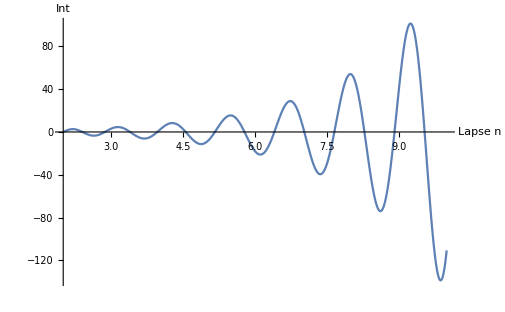

```mathematica
Plot[Re[Int/.{xa->0,xb->2,ta->0,tb->0,m->1,k->1,ℏ->0.1}],{n,2,10},PlotRange->All,AxesLabel->{n (Lapse), HoldForm[Int]},LabelStyle->{12, GrayLevel[0]}] (* Plot of the function showing oscillatory behavior *)
```

#### Find the saddle points:

```mathematica
Soln = Solve[D[Scl, n]==0, n] (* Finding the extrema, where C[1] is a constant integer, so there are infinitely many solutions *)
```

{{n→ConditionalExpression[(2 m (-ArcSinh[(k √(ta^2-2 ta tb+tb^2-xa^2+2 xa xb-xb^2))/(2 m)]+2 ⅈ π C[1]))/k,C[1]∈ℤ]},{n→ConditionalExpression[(2 m (ⅈ π-ArcSinh[(k √(ta^2-2 ta tb+tb^2-xa^2+2 xa xb-xb^2))/(2 m)]+2 ⅈ π C[1]))/k,C[1]∈ℤ]},{n→ConditionalExpression[(2 m (ArcSinh[(k √(ta^2-2 ta tb+tb^2-xa^2+2 xa xb-xb^2))/(2 m)]+2 ⅈ π C[1]))/k,C[1]∈ℤ]},{n→ConditionalExpression[(2 m (ⅈ π+ArcSinh[(k √(ta^2-2 ta tb+tb^2-xa^2+2 xa xb-xb^2))/(2 m)]+2 ⅈ π C[1]))/k,C[1]∈ℤ]}}

```mathematica
Clear[Sp,Sp1,Sp2,Sp3,Sp4,Test,Test1,Pl1,Pl2]
Clear[Pl2]
```

Attempt at using Manipulate function to test different saddle points corresponding to different choice of C:

```mathematica
(*Test1 = {xa->0,xb->6,ta-> 0, tb -> 4,m->1, k->1, C[1]->c1};*)
```

```mathematica
(*Sp0 = FullSimplify[Normal @ n/.Soln⟦1⟧/.Test1,c1∈Integers && c1∈Reals ]*)
```

```mathematica
(*Sp11 = FullSimplify[Normal @n/.Soln⟦1⟧/.Test1,c1∈Integers&& c1∈Reals ]*)
```

```mathematica
(*Sp22 = FullSimplify[Normal @n/.Soln⟦2⟧/.Test1,c1∈Integers&& c1∈Reals ]*)
```

```mathematica
(*Sp33 = FullSimplify[Normal @n/.Soln⟦3⟧/.Test1,c1∈Integers&& c1∈Reals ]*)
```

```mathematica
(*Sp44 = FullSimplify[Normal @n/.Soln⟦4⟧/.Test1,c1∈Integers&& c1∈Reals ]*)
```

```mathematica
(*ListPlot[{{Re[Sp11]/.c1->0,Im[Sp11]/.c1->0}(*,{Re[Sp22],Im[Sp22]},{Re[Sp33],Im[Sp33]},{Re[Sp44],Im[Sp44]}*)},PlotStyle->PointSize[Large], PlotRange->All]*)
```

```mathematica
(*Manipulate[
 ListPlot[{{Re[Sp11]/.c1->cc,Im[Sp11]/.c1->cc}(*,{Re[Sp22],Im[Sp22]},{Re[Sp33],Im[Sp33]},{Re[Sp44],Im[Sp44]}*)},PlotStyle->PointSize[Large], PlotRange->All],
{{cc,0},-10,10, 1}
]*)
```

Solve each conditional expression with given parameters and with different choices of C to check for the different saddle points. All the saddle points lie in two vertical lines equidistant from the imaginary axis on both sides (infinite number of saddle points). It turns out later that the saddle point of our concern is one of the four (the fourth one in the given sequence here) acquired by setting C=-1.

```mathematica
Test = {xa->0,xb->6,ta-> 0, tb -> 0,m->1, k->1,C[1]->-1};
```

```mathematica
Sp1 = FullSimplify[n/.Soln⟦1⟧/.Test]
```

-2 ⅈ (2 π+ArcSin[3])

```mathematica
Sp2 = FullSimplify[n/.Soln⟦2⟧/.Test]
```

-2 ⅈ (π+ArcSin[3])

```mathematica
Sp3 = FullSimplify[n/.Soln⟦3⟧/.Test ]
```

-3 ⅈ π+2 ArcCosh[3]

```mathematica
Sp4 = FullSimplify[n/.Soln⟦4⟧/.Test ]
```

-ⅈ (π+2 ArcCos[3])

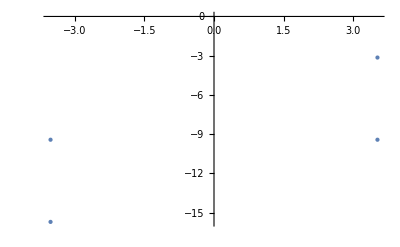

```mathematica
Pl1 = ListPlot[{{Re[Sp1],Im[Sp1]},{Re[Sp2],Im[Sp2]},{Re[Sp3],Im[Sp3]},{Re[Sp4],Im[Sp4]}},PlotStyle->PointSize[Large], PlotRange->All,LabelStyle->{12, GrayLevel[0]}] (* Plot the four saddle points with the given parameters and C=-1 *)
```

#### Make contour plots of the exponent to put the saddle points in context:

Contour plot of the real part of the exponent (Pl2) and the imaginary part of the exponent (Pl3), along with the saddle points (Replot and Implot). As before, we are not yet concerned with the complete function since the exponent suffices in allowing us to make the general approximation:

```mathematica
Pl2 = ContourPlot[Re[ⅈ Scl/.Test/.{n->nr+ⅈ ni}],{nr, -10, 10},{ ni, -10, 10}, ColorFunction->"TemperatureMap", Contours->100,LabelStyle->{12, GrayLevel[0]}] (* Contour plot of the real part of the exponent. *)
```

-Graphics-

```mathematica
Replot=Show[Pl2,Pl1] (* Showing with the saddle points *)
```

-Graphics-

```mathematica
Pl3 = ContourPlot[Im[ⅈ Scl/.Test/.{n->nr+ⅈ ni}],{nr, -10, 10},{ ni, -10, 10}, ColorFunction->"TemperatureMap", Contours->150,LabelStyle->{12, GrayLevel[0]}](* Contour plot of the imaginary part of the exponent. *)
```

-Graphics-

```mathematica
Implot=Show[Pl3,Pl1] (* Showing with the saddle points *)
```

-Graphics-

#### Find the lines of steepest descent/ascent:

```mathematica
Sp4
```

-ⅈ (π+2 ArcCos[3])

```mathematica
-ⅈ (π+2 ArcCos[√5])//N
```

2.88727-3.14159 ⅈ

Make a contour plot of the imaginary part of the exponent for the hopefully-relevant saddle point value of the exponent (Pl4). We are looking for lines of steepest descent/ascent, which have constant imaginary parts, so this allows us to see the lines of steepest descent/ascent that pass through the saddle point/s. Note that n is set to Sp4.

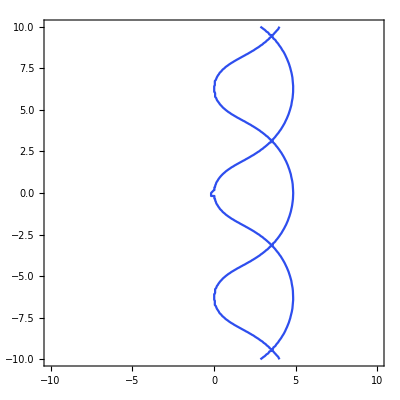

```mathematica
Pl4 = ContourPlot[Im[ⅈ Scl/.Test/.{n->nr+ⅈ ni}]==Im[ⅈ Scl/.Test/.{n->-ⅈ (π+2 ArcCos[3])}],{nr, -10, 10},{ ni, -10, 10}, ColorFunction->"TemperatureMap", Contours->150,LabelStyle->{12, GrayLevel[0]}] (* Contour plot of imaginary part of exponent evaluated at fourth saddle point *)
```

```mathematica
Lofda=Show[Pl2,Pl1,Pl4] (* Showing altogether the contour for the real part of the exponent (Pl2), the saddle point (Pl1), and the lines of steepest descent/ascent (Pl4) *)
```

-Graphics-

```mathematica
(*Pl5 = ContourPlot[Re[ⅈ Scl/.Test/.{n->nr+ⅈ ni}]==Re[ⅈ Scl/ⅇ^0/.Test/.{n->-ⅈ (π+2 ArcCos[√5])}],{nr, -10, 10},{ ni, -10, 10}, ColorFunction->"TemperatureMap", Contours->150]*)
```

#### Determine the relevant saddle point/s:

Now, we add a small perturbation to our seemingly endless line of steepest descent/ascent that stems from Sp4 (why?). Explain this step in greater detail. The perturbation is introduced by giving an imaginary component to ℏ (which is set to 1 for now) in the form of ⅇ^ⅈα where α is the perturbation parameter that can be varied to slightly shift the lines of steepest descent/ascent.

```mathematica
Manipulate[
Show[Pl2,Pl1,ContourPlot[Im[ⅈ Scl/.Test/.{n->nr+ⅈ ni}]==Im[ⅈ Scl/ⅇ^(ⅈ α)/.Test/.{n->-ⅈ (π+2 ArcCos[√5])}],{nr, -10, 10},{ ni, -10, 10}, ColorFunction->"TemperatureMap", Contours->150,LabelStyle->{12, GrayLevel[0]}]],
{{α,-0.01},-0.1,0.1}
] (* This is the same plot as Lofda except with a small perturbation. *)
```

Lines of steepest descent and ascent have constant imaginary parts - why?

#### Evaluate (or rather, approximate) the integral:

Plugging in the expression for  for n for the dominant saddle point (with C[1]=-1) into the expression that we are integrating gives us an approximation to the integral.

```mathematica
Cond={C[1]->-1, ta->0,tb->0,xa-> xb-l,m->1,k->1,ℏ->1}; (* Redefining xa and xb in terms of l=xb-xa *)
Cond1={C[1]->-1, ta->0,tb->0,xa-> xb-l,(*m->1,k->1,*)ℏ->1};
```

```mathematica
Spfin = FullSimplify[n/.Soln⟦4⟧/.Cond1] (* General expression for n at the dominant saddle point with given parameters *)
```

(2 m (-ⅈ π+ArcSinh[(k √(-l^2))/(2 m)]))/k

```mathematica
FullSimplify[Pref*Exp[ⅈ Scl]]/.Cond1 (* General form of integrand for kernel with given parameters *)
```

(2 ⅇ^(-1/4 ⅈ (2 m n-k l^2 Coth[(k n)/(2 m)])))/(√(-k^2 Csch[(k n)/(2 m)]^2))

```mathematica
g=FullSimplify[Exp[ⅈ Scl/ℏ]/.n->Spfin/.Cond1] (* Most general approximation of the integral using saddle point approx. (disregarding prefactor) *)
```

ⅇ^(-(ⅈ m (k √(-l^2) √(4-(k^2 l^2)/m^2)-4 ⅈ m π+4 m ArcSinh[(k √(-l^2))/(2 m)]))/(4 k))

```mathematica
Simplify[Im[ArcSinh[(k √(-l^2))/(2 m)]]/.{l->2m/k},Assumptions->{m>0,k>0}]
```

π/2

```mathematica
Simplify[Im[ArcSinh[(k √(-l^2))/(2 m)]],Assumptions->{l> 2m/k, l>0,m>0,k>0}]
```

Re[ArcSin[(k l)/(2 m)]]

```mathematica
Simplify[Im[ArcSinh[(k √(-(2m/k+1)^2))/(2 m)]],Assumptions->{l> 2m/k, l>0,m>0,k>0}]
```

Re[ArcSin[1+k/(2 m)]]

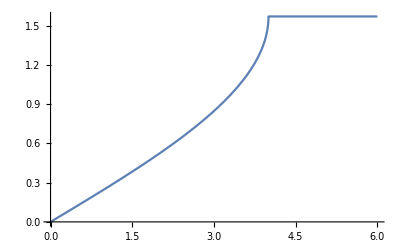

```mathematica
Plot[Im[ArcSinh[(k √(-l^2))/(2 m)]/.{m->2,k->1}],{l,0,6}]
```

For plotting purposes, let' s evaluate g with all parameters defined:

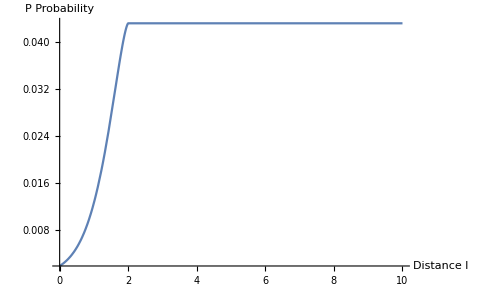

```mathematica
Plot[(Abs[g/.Cond])^2,{l,0,10},PlotRange->All, AxesLabel->{l (Distance), P (Probability)},LabelStyle->{12, GrayLevel[0]}] (* Plot of the probability approximation with respect to l (disregarding prefactor) *)
```

```mathematica
Lcrit=FullSimplify[Solve[D[(Abs[g])^2, l]==0, l]] (* Determining the critical distance between the particle and antiparticle (before which they remain virtual particles) *)
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

{{l→-(2 m)/k},{l→(2 m)/k}}

```mathematica
IntApprox = FullSimplify[g/.Lcrit⟦2⟧, m ∈Reals && m>0 && k∈ Reals && k>0]  (* Final approximation of kernel with critical distance and other given parameters *)
```

ⅇ^(-(m^2 π)/(2 k))

```mathematica
Prob = IntApprox^2 (* Final approximation of probability with *)
```

ⅇ^(-(m^2 π)/k)

Use n (saddle point) to plot trajectory.

```mathematica
Fcond={l->2m/k,k->1,m->1};
```

```mathematica
Cond1
Fcond
```

```mathematica
{C[1]->-1,ta->0,tb->0,xb->l+xa,ℏ->1}
```

{C[1]→-1,ta→0,tb→0,xb→l+xa,ℏ→1}

```mathematica
nn=FullSimplify[n/.Soln⟦4⟧/.Cond1//.Fcond]
```

-ⅈ π

Lookup de Sitter in Poincare patch (in proper time coordinates and in conformal (time) coordinates)

```mathematica
-dtau^2=ds^2 = -dt^2 + spatial part
= -f(η) dη^2 + spatial part
```

Find derivative of imaginary part of T with respect to internal time, and check which choice of parameters give you negative derivative
ParametricPlot3D for imaginary time, real time, and real x.

```mathematica
Cond2={xa->0,xb->1,ta->0,tb->0,m->1,k->1};
```

```mathematica
ParametricPlot3D[{Re[xm//.n->(2 m (-ⅈ π+ArcSinh[(k √(ta^2-2 ta tb+tb^2-xa^2+2 xa xb-xb^2))/(2 m)]))/k//.Cond2],Im[tm//.n->(2 m (-ⅈ π+ArcSinh[(k √(ta^2-2 ta tb+tb^2-xa^2+2 xa xb-xb^2))/(2 m)]))/k//.Cond2],Re[tm//.n->(2 m (-ⅈ π+ArcSinh[(k √(ta^2-2 ta tb+tb^2-xa^2+2 xa xb-xb^2))/(2 m)]))/k//.Cond2]},{T,0,1},AxesLabel->{Real x, Imaginary t, Real t},LabelStyle->{12, GrayLevel[0]}]
```

-Graphics3D-